# Potential V(q) - minimum study

## Compare the analytical and numerical results of the 1^st order derivative of V.

Moments of inertia & constants

```mathematica
I1=20;
I2=100;
I3=40;
j=6.5;
θ=30;
spin=N[45/2];
```

Inertia factors & a.m. components

```mathematica
A1=1/(2*I1);
A2=1/(2*I2);
A3=1/(2*I3);
Subscript[j, 1][th_]:=N[j*Cos[th*π/180]];
Subscript[j, 2][th_]:=N[j*Sin[th*π/180]];
```

Rotor functions

```mathematica
aFct[th_]:=A2(1-(Subscript[j, 2][th])/spin)-A1;
uFct[th_]:=(A3-A1)/aFct[th];
v0Fct[th_]:=-(A1*Subscript[j, 1][th])/aFct[th];
kFct[th_]:=√uFct[th];
kPrimeFct[th_]:=√(1-kFct[th]^2);
```

Elliptic variables

```mathematica
s[q_,k_]:=If[Im[JacobiSN[q,k^2]]==0,Re[JacobiSN[q,k^2]]];
c[q_,k_]:=If[Im[JacobiCN[q,k^2]]==0,Re[JacobiCN[q,k^2]]];
d[q_,k_]:=√(1-k^2*s[q,k]^2);
```

## Rotor potential V(q) - single variable created

```mathematica
(* Declare functions for initalizing the helper functions *)
k=kFct[θ];
kPrime=kPrimeFct[θ];
v0=v0Fct[θ];
V[q_]:=(spin(spin+1)*k^2+v0^2)s[q,k]^2+(2spin+1)*v0*c[q,k]*d[q,k];
```

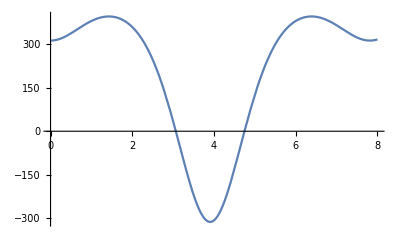

```mathematica
Plot[V[q],{q,0,8}]
```

## Analytical expression for V’(q)

```mathematica
Vprime[q_]:=s[q,k]*((spin(spin+1)k^2+v0^2)2*c[q,k]*d[q,k]-(2spin+1)v0*kPrime^2-(2spin+1)v0*2*k^2*c[q,k]^2);
```

## Generate numerical data as tables

```mathematica
h=0.1;
potential=Table[{q,V[q]},{q,-8,8,0.1}];
derivAnalytic=Table[{q,Vprime[q]},{q,-8,8,0.1}];
derivNumeric=Table[{q,N[(-V[q+2h]+8V[q+h]-8V[q-h]+V[q-2h])/(12h)]},{q,-8,8,0.1}];
```

## Graphical representation of the functions

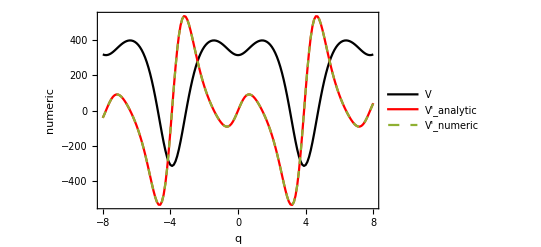

```mathematica
ListPlot[{potential,derivAnalytic,derivNumeric},Joined->True,Frame->True,FrameLabel->{"q","numeric"},PlotLegends->Placed[{"V","V'_analytic","V'_numeric"},{0.50,0.2}],PlotStyle->{{Black},{Red},{Dashed}}]
```